# How to use

## setup

### general

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
(*<<MaTeX`(* for beautiful figures*)*)
```

```mathematica
(*translate the normalized power spectrum to C_l (μK)^2*)
TomuK2 = (2.7255*10^6)^2
```

7.42835×10^12

### Import expansion history of universe

```mathematica
(*Import the background expansion history calculated by CLASS code*)
```

```mathematica
background=Import["data_axion/CLASS_data_background.dat"];
background[[4]]
bg7 = Drop[background,4];
```

{#,1:z,2:proper,time,[Gyr],3:conf.,time,[Mpc],4:H,[1/Mpc],5:comov.,dist.,6:ang.diam.dist.,7:lum.,dist.,8:comov.snd.hrz.,9:(.)rho_g,10:(.)rho_b,11:(.)rho_cdm,12:(.)rho_lambda,13:(.)rho_ur,14:(.)rho_crit,15:(.)rho_tot,16:(.)p_tot,17:(.)p_tot_prime,18:gr.fac.,D,19:gr.fac.,f}

```mathematica
(* Construct the functions to translate various time variables  *)
```

```mathematica
z2HubbleList = Transpose[{Transpose[bg7][[1]],Transpose[bg7][[4]]  }];
z2Hubble = Interpolation[z2HubbleList]
```

InterpolatingFunction[…]

```mathematica
tau2HubbleList = Transpose[{Transpose[bg7][[3]],Transpose[bg7][[4]]  }];
tau2Hubble = Interpolation[tau2HubbleList]
```

InterpolatingFunction[…]

```mathematica
Gyr2Mpc = QuantityMagnitude["Gigayears"*"SpeedOfLight","Megaparsecs"]
```

(5995849160 π)/61478577

```mathematica
(*physical time in Mpc*)
time2HubbleList = Transpose[{Gyr2Mpc*Transpose[bg7][[2]],Transpose[bg7][[4]]  }];
time2Hubble = Interpolation[time2HubbleList]
```

InterpolatingFunction[…]

```mathematica
z2timeList = Transpose[{Transpose[bg7][[1]],Gyr2Mpc*Transpose[bg7][[2]]  }];
z2time = Interpolation[z2timeList]
```

InterpolatingFunction[…]

```mathematica
(*Conformal time in Mpc*)
time2tauList = Transpose[{Gyr2Mpc*Transpose[bg7][[2]],Transpose[bg7][[3]]  }];
time2tau= Interpolation[time2tauList]
```

InterpolatingFunction[…]

```mathematica
tau2timeList = Transpose[{Transpose[bg7][[3]],Gyr2Mpc*Transpose[bg7][[2]]  }];
tau2time= Interpolation[tau2timeList]
```

InterpolatingFunction[…]

```mathematica
z2tauList = Transpose[{Transpose[bg7][[1]],Transpose[bg7][[3]]  }];
z2tau = Interpolation[z2tauList]
```

InterpolatingFunction[…]

```mathematica
tau2zList = Transpose[{Transpose[bg7][[3]],Transpose[bg7][[1]]  }];
tau2z = Interpolation[tau2zList]
```

InterpolatingFunction[…]

### Solver for axion dynamics

We solve the Equation of Motion for the axion field.
We normalize the axion field as 
phi[t] = ϕ[t]/ϕ_in,
where ϕ is a physical field amplitude, ϕ_in is its initial value, and phi is a normalized value, which we will estimate.

```mathematica
(*potential of the axion field. *)
Vaxion[phi_,m_] = m^2/2 phi^2;
dVaxion[phi_,m_] = D[Vaxion[phi,m],phi]
```

m^2 phi

```mathematica
(*
m: mass of axion in eV

Note that the conformal time and Hubble parameter are in Mpc
*)
```

```mathematica
InitialRedshift = 10^6 ;
timeini = z2time[InitialRedshift](*Mpc*);
```

```mathematica
eV2MpcInv=QuantityMagnitude[ "Electronvolts"/"ReducedPlanckConstant"/"SpeedOfLight",1/"Megaparsecs"];
```

```mathematica
(*Define the solver for axion dynamics*)
```

```mathematica
solutionPhi[mass_(*eV*)] := phi/.NDSolve[{
0==phi''[t]+3 time2Hubble[t]phi'[t]+(eV2MpcInv)^2 dVaxion[phi[t],mass] ,
phi'[timeini]==0,phi[timeini]==1},
phi,{t,timeini,z2time[0]},
MaxStepSize->(*0.1*)0.01(2Pi)/(eV2MpcInv*mass)][[1]]
```

### Export function of axion dynamics

We export the axion field value over times, which  will be used in CLASS code.

We normalize the axion energy density as $phi_{initial}=1$. 

		   - mass    : axion mass in eV
	- Ntau    : number of bins of conformal time 
	- tau[i]:  bins for conformal time 

We divide the conformal time as 
	tau[i_ ] =tau0 (i+1)/Ntau (i=1,Ntau-1)
, where tau0=z2tau[0] is current conformal time

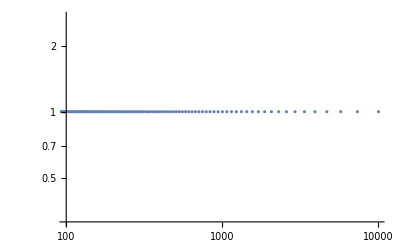

```mathematica
(*We need Ntau=10^3 at least to follow the CMB physics while the heavy axion requires larger Ntau.
We reccomend Ntau=10^4 for the case of  m\sim 10^{-28}eV.
See the number of bins near z\sim 10^3.
 *)
ListLogLogPlot[
Table[{tau2z[i z2tau[0]/10^3],1},{i,1,10^3}]
,PlotRange->{{100,10^4},All}
]
```

```mathematica
(*Construct a table of axion dynamics for a given parameters.*)
```

```mathematica
exportAxionDynamics[mass_(*eV*),Ntau_]:=Module[{tau0,taulist,solphi,philist},
tau0 = z2tau[0];
taulist = Table[tau0 (i+1)/Ntau,{i,0,Ntau-1}];
solphi=solutionPhi[mass(*eV*)] ;

philist = solphi[ tau2time[taulist] ];  (*Table[solphi[tau2time[tauBin[i]]],{i,0,totNUMtau-1}];*)



(*check resolution*)
Print[
Show[
LogLinearPlot[solphi[z2time[z]], {z,10,4000},PlotRange->{ {10,2000},{-0.5,1.1}}],
ListLogLinearPlot[Transpose[{tau2z[taulist],philist}],PlotStyle->Red]
]
];
Export["data_axion/axionDynamics_m"<>ToString[Round[-100*Log[10,mass]]]<>"_N"<>ToString[Ntau]<>".dat",philist]
]
```

```mathematica
(*Examples:*)
```

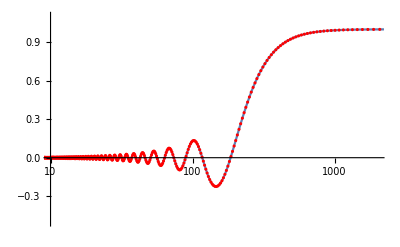

data_axion/axionDynamics_m2900_N1000.dat

```mathematica
exportAxionDynamics[10^-29,10^3]
```

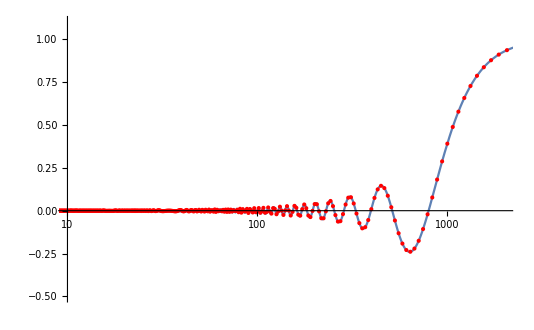

data_axion/axionDynamics_m2800_N1000.dat

```mathematica
exportAxionDynamics[10^-28,10^3]
```

### Function to call birefCLASS

Here, we construct the function to prepare the axion dynamics, run the CLASS code, and gather the output C_l EE,EB,BB data.
$alpha0 = -g*ϕ_in/2$ represents the strength of the cosmic birefringence. 
Thus, the polarization rotation angle is written as 
$alpha(t) = -g*(ϕ(t)-ϕ_obs)/2 = alpha0 ( phi(t) - phi_obs  )$

At first, the .ini file for the birefCLASS is written in the following way:

```mathematica
(*this function returns the filename of the exported file.*)
iniBirefCLASS[mass_(*eV*),Ntau_, alpha0_,signOFm_(*=+1,-1*)]:=Module[{defaultIniFile,IsMminus,IsMminusIndex,filename},
defaultIniFile = Import["data_axion/biref_default.ini","text"];
IsMminus = If[signOFm<0,"yes","no"];
IsMminusIndex = If[signOFm<0,"-","+"];

filename = "alpha0"<>ToString[Round[10^4 alpha0]]<>
"_m"<>ToString[Round[-100*Log[10,mass]]]<>
"_N"<>ToString[Ntau]<>
IsMminusIndex;

Export[
filename<>".ini",
"filename_axion_dynamics=data_axion/"<>"axionDynamics_m"<>ToString[Round[-100*Log[10,mass]]]<>"_N"<>ToString[Ntau]<>".dat\n"<>
"length_resolution_axion_dynamics="<>ToString[Ntau]<>"\n"<>
"isotropic_alpha_0="<>ToString[alpha0]<>"\n"<>
"is_m_minus="<>IsMminus<>"\n"<>
"root = output/"<>filename<>
defaultIniFile,

"text"];
filename
]
```

```mathematica
(*example*)
```

```mathematica
nameExample=iniBirefCLASS[10^-31.5,200, 0.1,-1]
nameExample
```

alpha01000_m3150_N200-

alpha01000_m3150_N200-

As we prepare two .ini files, we run CLASS twice to evaluate the mode functions with m=+2 and m=-2.
After the calculation, we gather  two results and combine C_l in the following way

```mathematica
CombinedCls[filenamePlus_,filenameMinus_] := Module[{
Clscalar,CltPlus,CltMinus,
 listl,ClsEE,ClsBB,ClsEB,ClsTB,
CltPlusEE,CltPlusBB,CltPlusEB,CltPlusTB,
CltMinusEE,CltMinusBB,CltMinusEB,CltMinusTB
},

(*Read both scalar C_l (m=0), tenser C_ls (m=+2,-2)  *)
Clscalar  = Drop[Import[filenamePlus<>"cls.dat","Table"],11];
CltPlus =  Drop[Import[filenamePlus<>"clt.dat","Table"],11];
CltMinus =  Drop[Import[filenameMinus<>"clt.dat","Table"],11];

listl = Transpose[Clscalar][[1]];

ClsEE= TomuK2*Transpose[Clscalar][[3]];
ClsBB= TomuK2*Transpose[Clscalar][[5]] ;
ClsEB= TomuK2*Transpose[Clscalar][[6]] ;
ClsTB= TomuK2*Transpose[Clscalar][[7]];

CltPlusEE=TomuK2*Transpose[CltPlus][[3]] ;
CltPlusBB= TomuK2*Transpose[CltPlus][[5]] ;
CltPlusEB= TomuK2*Transpose[CltPlus][[6]] ;
CltPlusTB= TomuK2*Transpose[CltPlus][[7]] ;

CltMinusEE=TomuK2*Transpose[CltMinus][[3]];
CltMinusBB= TomuK2*Transpose[CltMinus][[5]];
CltMinusEB= TomuK2*Transpose[CltMinus][[6]];
CltMinusTB= TomuK2*Transpose[CltMinus][[7]];

(* Combine the scalar and tenser modes *)
 Join[
{{"l","EE", "BB", "EB","TB"}},
Transpose[{listl,
ClsEE+ 1/2(CltPlusEE+CltMinusEE),   
ClsBB+ 1/2(CltPlusBB+CltMinusBB),   
ClsEB+ 1/2(CltPlusEB+CltMinusEB),   
ClsTB+ 1/2(CltPlusTB+CltMinusTB)
}]
]

]
```

Finally, we define a function to run CLASS with axion dynamics.

```mathematica
birefCLASS[mass_(*eV*),Ntau_, alpha0_] := Module[{defaultIniFile,filenamePlus, filenameMinus,ClsBirefList},
(*prepare the axion dynamics table in "/data_axion/"*)
exportAxionDynamics[mass,Ntau];

(*prepare the .ini files to run the CLASS code*)
filenamePlus  = iniBirefCLASS[mass(*eV*),Ntau, alpha0,+1(*=+1,-1*)];
filenameMinus = iniBirefCLASS[mass(*eV*),Ntau, alpha0,-1(*=+1,-1*)];

(*run the birefCLASS*)
Run["./class "<>filenamePlus<>".ini cl_ref_biref.pre"];
Run["./class "<>filenameMinus<>".ini cl_ref_biref.pre"];

(*gather the CLASS results *)
ClsBirefList = CombinedCls["output/"<>StringReplace[filenamePlus,".ini"-> ""],"output/"<>StringReplace[filenameMinus,".ini"-> ""]] ;
(*export the birefCLASS result*)
Export["data_axion/Cl_birefringence_"<>StringDrop[filenamePlus,-1]<>".dat",ClsBirefList];

ClsBirefList
]
```

```mathematica
(*example*)
```

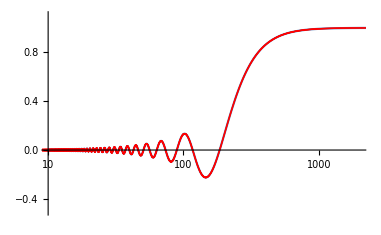

{{l,EE,BB,EB,TB},{2,0.0321974,2.79528×10^-10,2.30841×10^-6,0.000418338},2497,{2500,2.80495,0.00111006,0.0557868,-0.0316682}}
 |  |  |  |

```mathematica
results = birefCLASS[10^-29,10^4,0.01]
```

{1}
 |  |  |  |

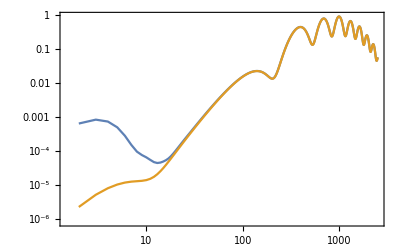

```mathematica
transposeresult = Transpose[Drop[results,1]]
ListLogLogPlot[
{
Transpose[{transposeresult[[1]],0.02transposeresult[[2]]}],
Transpose[{transposeresult[[1]],transposeresult[[4]]}]
}
,Joined->True,Frame->True
]
```

### Function to call birefCLASS with high precision

We also define birefCLASS with choosing the  precision parameter file, `cl_ref _birefA.pre` and `cl_ref _birefB.pre`.
This option, however, requires large run time. 
Thus, it is used only for checking the resolution.

```mathematica
birefCLASSpreciseA[mass_(*eV*),Ntau_, alpha0_] := Module[{defaultIniFile,filenamePlus, filenameMinus,ClsBirefList},
(*prepare the axion dynamics table in "/data_axion/"*)
exportAxionDynamics[mass,Ntau];

(*prepare the .ini files to run the CLASS code*)
filenamePlus  = iniBirefCLASS[mass(*eV*),Ntau, alpha0,+1(*=+1,-1*)];
filenameMinus = iniBirefCLASS[mass(*eV*),Ntau, alpha0,-1(*=+1,-1*)];

(*run the birefCLASS*)
Run["./class "<>filenamePlus<>".ini cl_ref_birefA.pre"];
Run["./class "<>filenameMinus<>".ini cl_ref_birefA.pre"];


(*gather the CLASS results *)
ClsBirefList = CombinedCls["output/"<>StringReplace[filenamePlus,".ini"-> ""],"output/"<>StringReplace[filenameMinus,".ini"-> ""]] ;
(*export the birefCLASS result*)
Export["data_axion/Cl_precise_birefringence_"<>StringDrop[filenamePlus,-1]<>".dat",ClsBirefList];

ClsBirefList
]
```

```mathematica
birefCLASSpreciseB[mass_(*eV*),Ntau_, alpha0_] := Module[{defaultIniFile,filenamePlus, filenameMinus,ClsBirefList},
(*prepare the axion dynamics table in "/data_axion/"*)
exportAxionDynamics[mass,Ntau];

(*prepare the .ini files to run the CLASS code*)
filenamePlus  = iniBirefCLASS[mass(*eV*),Ntau, alpha0,+1(*=+1,-1*)];
filenameMinus = iniBirefCLASS[mass(*eV*),Ntau, alpha0,-1(*=+1,-1*)];

(*run the birefCLASS*)
Run["./class "<>filenamePlus<>".ini cl_ref_birefB.pre"];
Run["./class "<>filenameMinus<>".ini cl_ref_birefB.pre"];


(*gather the CLASS results *)
ClsBirefList = CombinedCls["output/"<>StringReplace[filenamePlus,".ini"-> ""],"output/"<>StringReplace[filenameMinus,".ini"-> ""]] ;
(*export the birefCLASS result*)
Export["data_axion/Cl_precise_birefringence_"<>StringDrop[filenamePlus,-1]<>".dat",ClsBirefList];

ClsBirefList
]
```

```mathematica
(*Here, you can compare the birefCLASS and birefCLASSprecise, while it takes a long time.*)
```

```mathematica
(*resultsPrecise = birefCLASSprecise[10^-29,10^3,0.01] 
transposeresult = Transpose[results];
transposeresultP = Transpose[resultsPrecise];
ListLogLogPlot[
{
Transpose[{transposeresult[[1]],0.02transposeresult[[2]]}],
Transpose[{transposeresult[[1]],transposeresult[[4]]}],
Transpose[{transposeresultP[[1]],transposeresultP[[4]]}]
}
,Joined->True,PlotStyle->{Black, {Red,Dotted},{Blue,Dashed}}
]*)
```

### Function to call birefCLASS for step-function case

We consider a step-type polarization rotation as a toy model.
Considering the definition of the rotation angle, 
$alpha(t) = -g*(ϕ(t)-ϕ_obs)/2 = alpha0 ( phi(t) - phi_obs  )$,
here we take 
alpha0 =1, and 
phi(t)  = betarec (z>10),  betarei (0< z<10), and 0 (z=0)

```mathematica
exportStepType[betarei_,betarec_,Ntau_]:=Module[{tau0,taulist,stepfunction,philist},
tau0 = z2tau[0];
taulist = Table[tau0 (i+1)/Ntau,{i,0,Ntau-1}];
stepfunction[z_]= Which[
z>10,betarec,
z>tau2z[z2tau[0]],betarei,
z==tau2z[z2tau[0]], 0
];

philist =  stepfunction/@tau2z[taulist]; (*Table[solphi[tau2time[tauBin[i]]],{i,0,totNUMtau-1}];*)


(*check resolution*)
Print[
ListLogLinearPlot[Transpose[{tau2z[taulist],philist}],PlotStyle->Red,Frame-> True]
];
Export["data_axion/steptype_betarec"<>ToString[Round[10^4 betarec]]<>"_betarei"<>ToString[Round[10^4 betarei]]<>"_N"<>ToString[Ntau]<>".dat",philist]
]
```

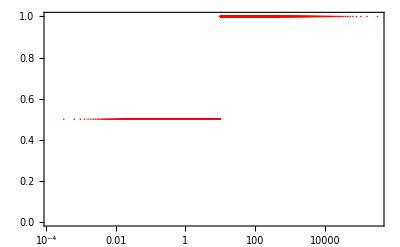

data_axion/steptype_betarec10000_betarei5000_N10000.dat

```mathematica
(*Example*)
exportStepType[0.5,1,10^4]
```

```mathematica
(*this function returns the filename of the exported file.*)
iniBirefCLASSstep[betarei_,betarec_,Ntau_, signOFm_(*=+1,-1*)]:=Module[{defaultIniFile,IsMminus,IsMminusIndex,filename},
defaultIniFile = Import["data_axion/biref_default.ini","text"];
IsMminus = If[signOFm<0,"yes","no"];
IsMminusIndex = If[signOFm<0,"-","+"];

filename = "betarec"<>ToString[Round[10^4 betarec]]<>
"_betarei"<>ToString[Round[10^4 betarei]]<>
"_N"<>ToString[Ntau]<>
IsMminusIndex;

Export[
filename<>".ini",
"filename_axion_dynamics=data_axion/"<>"steptype_betarec"<>ToString[Round[10^4 betarec]]<>"_betarei"<>ToString[Round[10^4 betarei]]<>"_N"<>ToString[Ntau]<>".dat\n"<>
"length_resolution_axion_dynamics="<>ToString[Ntau]<>"\n"<>
"isotropic_alpha_0="<>ToString[1.0]<>"\n"<>
"is_m_minus="<>IsMminus<>"\n"<>
"root = output/"<>filename<>
defaultIniFile,

"text"];
filename
]
```

```mathematica
birefCLASSstep[ betarei_,betarec_,Ntau_] := Module[{defaultIniFile,filenamePlus, filenameMinus,ClsBirefList},
(*prepare the axion dynamics table in "/data_axion/"*)
exportStepType[betarei,betarec,Ntau];

(*prepare the .ini files to run the CLASS code*)
filenamePlus  =iniBirefCLASSstep[betarei,betarec,Ntau, +1(*=+1,-1*)];
filenameMinus = iniBirefCLASSstep[betarei,betarec,Ntau, -1(*=+1,-1*)];


(*run the birefCLASS*)
Run["./class "<>filenamePlus<>".ini cl_ref_biref.pre"];
Run["./class "<>filenameMinus<>".ini cl_ref_biref.pre"];

(*gather the CLASS results *)
ClsBirefList = CombinedCls["output/"<>StringReplace[filenamePlus,".ini"-> ""],"output/"<>StringReplace[filenameMinus,".ini"-> ""]] ;
(*export the birefCLASS result*)
Export["data_axion/Cl_birefringence_"<>StringDrop[filenamePlus,-1]<>".dat",ClsBirefList];

ClsBirefList
]
```

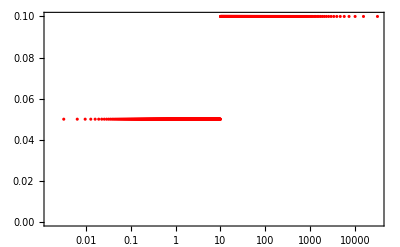

{{l,EE,BB,EB,TB},{2,0.0318724,0.000323682,0.00321192,0.267719},2496,{2499,2.68326,0.110312,0.543924,-0.312622},{2500,2.69531,0.110807,0.546366,-0.315237}}
 |  |  |  |

```mathematica
(*Example*)
test = birefCLASSstep[ 0.05,0.1,10^3]
```

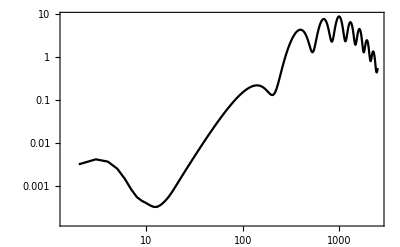

```mathematica
l2ClEB[table_]:= Transpose[{ Transpose[table][[1]],Transpose[table][[4]]}];
ListLogLogPlot[
{l2ClEB[test]}
,Joined->True,PlotStyle->{Black},Frame->True
]
```

## Demo

### C_lEB for Axion Dynamics

```mathematica
l2ClEB[table_]:= Drop[Transpose[{ Transpose[table][[1]],Transpose[table][[4]]}],1];
l2ClEE[table_]:= Drop[Transpose[{ Transpose[table][[1]],Transpose[table][[2]]}],1];
```

```mathematica
vNtau = 2*10^4;
valpha0 = 0.1;
```

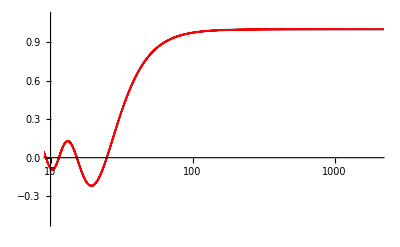

{{l,EE,BB,EB,TB},{2,0.0321915,5.37207×10^-8,0.0000352414,0.00553307},2497,{2500,2.69478,0.111337,0.547617,-0.315993}}
 |  |  |  |

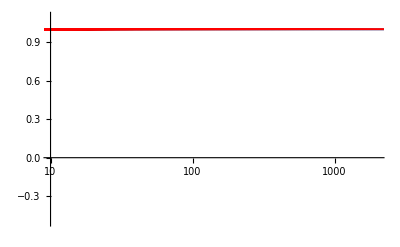

{{l,EE,BB,EB,TB},{2,0.0311619,0.0010024,0.00558282,0.431025},2496,{2499,2.68583,0.107745,0.537813,-0.308962},{2500,2.69789,0.108228,0.540228,-0.311547}}
 |  |  |  |

```mathematica
(*data*)
casem303 = birefCLASS[10^-30.3(*eV*),vNtau,valpha0] 
casem323 = birefCLASS[10^-32.3(*eV*),vNtau,valpha0]
```

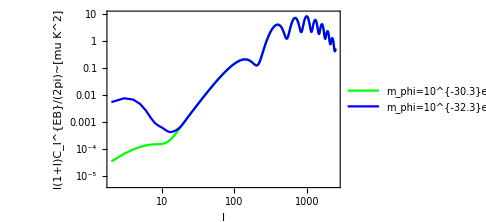

```mathematica
(*Plot ClEB*)
ListLogLogPlot[ 
{l2ClEB[casem303],l2ClEB[casem323] },
PlotStyle->{Green, Blue, Red,Black},
PlotLegends->{
"m_phi=10^{-30.3}eV",
"m_phi=10^{-32.3}eV"
}
,
PlotRange-> {{2,2500},{10^-5.3,10}},Joined->True,Frame->True,ImageSize->Medium,
FrameLabel->{"l"
,"l(1+l)C_l^{EB}/(2pi)~[mu K^2]"}
]
```

## Check precision

The birefCLASS depends on two precision parameters, Ntau and perturb_sampling_stepsize.
Ntau is a sampling step size of the axion dynamics, and perturb_sampling_stepsize is a time step to calculate the fluctuations in CLASS.
In general, the heavy axions requires better precision to calculate.

### m = 10^-29

```mathematica
massA = 10^-29(*eV*) ;
alpha0A = 0.01;
```

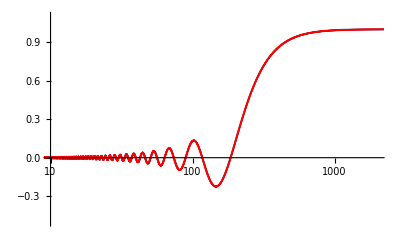

{{l,EE,BB,EB,TB},{2,0.0321974,2.79467×10^-10,2.30795×10^-6,0.000418306},2496,{2499,2.79241,0.0011051,0.0555373,-0.0314075},{2500,2.80495,0.00111006,0.0557868,-0.0316682}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321974,2.79462×10^-10,2.30793×10^-6,0.000418301},2496,{2499,2.79241,0.0011051,0.0555373,-0.0314075},{2500,2.80495,0.00111006,0.0557868,-0.0316682}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321986,2.80523×10^-10,2.31476×10^-6,0.000418986},2496,{2499,2.79241,0.0011051,0.0555373,-0.0314076},{2500,2.80495,0.00111006,0.0557868,-0.0316683}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321992,2.80161×10^-10,2.31265×10^-6,0.000418738},2496,{2499,2.79242,0.0011051,0.0555373,-0.0314077},{2500,2.80495,0.00111006,0.0557869,-0.0316684}}
 |  |  |  |

```mathematica
case1 = birefCLASS[massA,2*10^4,alpha0A]  (*perturb_sampling_stepsize=0.04*)
case2 = birefCLASS[massA,2*10^5,alpha0A] 
case3 = birefCLASSpreciseA[massA,2*10^4,alpha0A] (*perturb_sampling_stepsize=0.01*)
case4 = birefCLASSpreciseB[massA,2*10^4,alpha0A] (*perturb_sampling_stepsize=0.005*)
```

```mathematica
(*show 3 cases*)
```

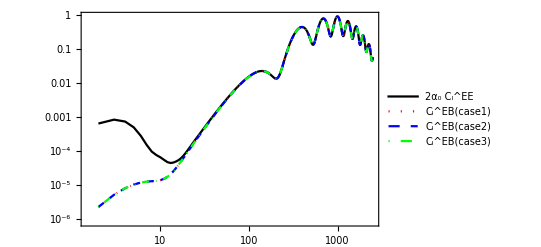

```mathematica
l2ClEB[table_]:= Transpose[{ Transpose[table][[1]],Transpose[table][[4]]}];
l2ClEE2alpha0[table_]  := Transpose[{ Transpose[table][[1]],2alpha0A*Transpose[table][[2]]}];

ListLogLogPlot[
{
l2ClEE2alpha0[Drop[case1,1]],
l2ClEB[Drop[case1,1]],
l2ClEB[Drop[case2,1]],
l2ClEB[Drop[case3,1]]
}
,Joined->True,PlotStyle->{Black, {Red,Dotted},{Blue,Dashed},{Green,DotDashed}},
PlotLegends-> {"2α_0 C_l^EE ", "C_l^EB(case1)", "C_l^EB(case2)", "C_l^EB(case3)"},PlotRange->All,Frame->True
]
```

```mathematica
(*compare 3 cases*)
```

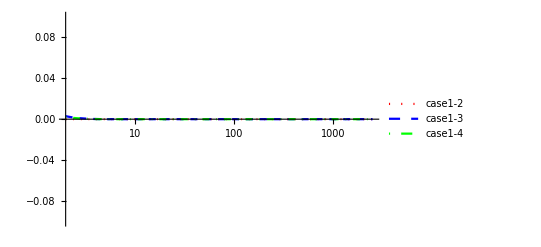

```mathematica
ClEBcase1  = Interpolation[Transpose[{ Transpose[Drop[case1,1]][[1]],Transpose[Drop[case1,1]][[4]]}]];
ClEBcase2 = Interpolation[Transpose[{ Transpose[Drop[case2,1]][[1]],Transpose[Drop[case2,1]][[4]]}]];
ClEBcase3 = Interpolation[Transpose[{ Transpose[Drop[case3,1]][[1]],Transpose[Drop[case3,1]][[4]]}]];
ClEBcase4 = Interpolation[Transpose[{ Transpose[Drop[case4,1]][[1]],Transpose[Drop[case4,1]][[4]]}]];

LogLinearPlot[
{
(ClEBcase2[l]-ClEBcase1[l])/ClEBcase1[l], (ClEBcase3[l]-ClEBcase1[l])/ClEBcase1[l], (ClEBcase4[l]-ClEBcase1[l])/ClEBcase1[l]
}
,{l,2,2500},PlotStyle->{{Red,Dotted},{Blue,Dashed},{Green,DotDashed}},
PlotLegends-> {"case1-2", "case1-3","case1-4"},PlotRange->{All,{-0.1,0.1}}
]
```

### m = 10^-27.9

```mathematica
massA = 10^-27.9(*eV*) ;
alpha0A = 0.01;
```

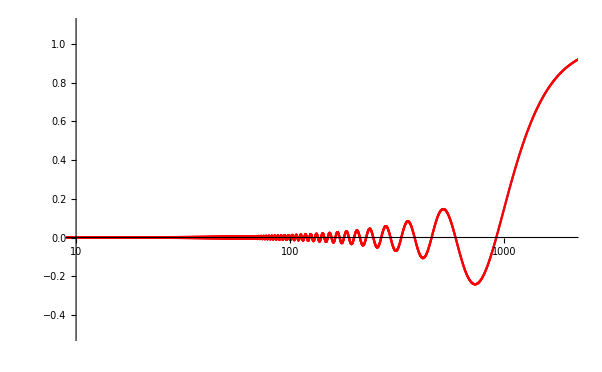

{{l,EE,BB,EB,TB},{2,0.0321975,3.04563×10^-12,2.39019×10^-7,0.0000438544},2496,{2499,2.79342,0.000103098,0.0166547,-0.0197502},{2500,2.80596,0.000103701,0.0167485,-0.0197227}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321975,3.03283×10^-12,2.38121×10^-7,0.0000437883},2496,{2499,2.79342,0.000103098,0.0166547,-0.0197503},{2500,2.80596,0.000103701,0.0167486,-0.0197228}}
 |  |  |  |

```mathematica
case1 = birefCLASS[massA,2*10^4,alpha0A] 
case2 = birefCLASS[massA,2*10^5,alpha0A] 
case3 = birefCLASSpreciseA[massA,2*10^4,alpha0A] 
case4 = birefCLASSpreciseB[massA,2*10^4,alpha0A]
```

```mathematica
(*show 3 cases*)
```

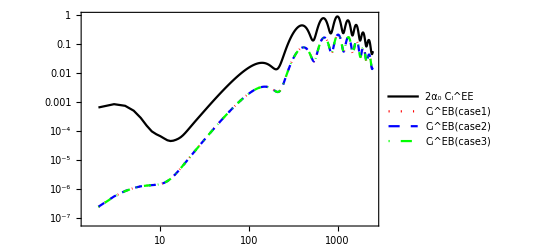

```mathematica
l2ClEB[table_]:= Transpose[{ Transpose[table][[1]],Transpose[table][[4]]}];
l2ClEE2alpha0[table_]  := Transpose[{ Transpose[table][[1]],2alpha0A*Transpose[table][[2]]}];

ListLogLogPlot[
{
l2ClEE2alpha0[Drop[case1,1]],
l2ClEB[Drop[case1,1]],
l2ClEB[Drop[case2,1]],
l2ClEB[Drop[case3,1]]
}
,Joined->True,PlotStyle->{Black, {Red,Dotted},{Blue,Dashed},{Green,DotDashed}},
PlotLegends-> {"2α_0 C_l^EE ", "C_l^EB(case1)", "C_l^EB(case2)", "C_l^EB(case3)"},PlotRange->All,Frame->True
]
```

```mathematica
(*compare 3 cases*)
```

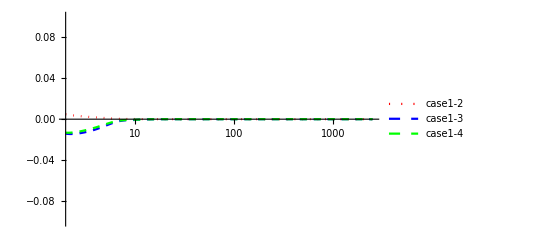

```mathematica
ClEBcase1  = Interpolation[Transpose[{ Transpose[Drop[case1,1]][[1]],Transpose[Drop[case1,1]][[4]]}]];
ClEBcase2 = Interpolation[Transpose[{ Transpose[Drop[case2,1]][[1]],Transpose[Drop[case2,1]][[4]]}]];
ClEBcase3 = Interpolation[Transpose[{ Transpose[Drop[case3,1]][[1]],Transpose[Drop[case3,1]][[4]]}]];
ClEBcase4 = Interpolation[Transpose[{ Transpose[Drop[case4,1]][[1]],Transpose[Drop[case4,1]][[4]]}]];

LogLinearPlot[
{
(ClEBcase2[l]-ClEBcase1[l])/ClEBcase1[l], (ClEBcase3[l]-ClEBcase1[l])/ClEBcase1[l], (ClEBcase4[l]-ClEBcase1[l])/ClEBcase1[l]
}
,{l,2,2500},PlotStyle->{{Red,Dotted},{Blue,Dashed},{Green,Dashed}},
PlotLegends-> {"case1-2", "case1-3","case1-4"},PlotRange->{All,{-0.1,0.1}}
]
```

### m = 10^-27.5

```mathematica
massA = 10^-27.5(*eV*) ;
alpha0A = 0.01;
```

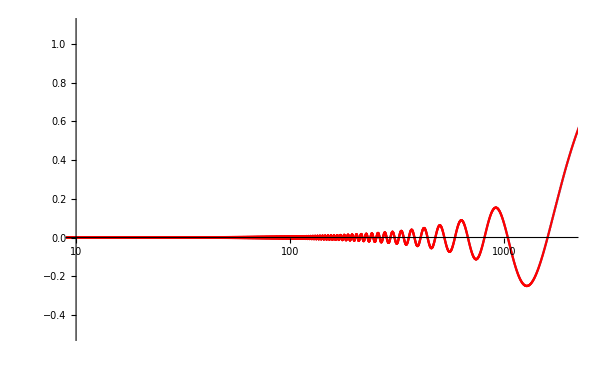

{{l,EE,BB,EB,TB},{2,0.0321975,5.38288×10^-14,3.32116×10^-8,5.7099×10^-6},2497,{2500,2.80605,0.0000114555,-0.00470653,0.0124995}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321975,5.27783×10^-14,3.25949×10^-8,5.68172×10^-6},2497,{2500,2.80605,0.0000114567,-0.00470673,0.0125004}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321987,5.32164×10^-14,3.28633×10^-8,5.6924×10^-6},2497,{2500,2.80605,0.0000114555,-0.00470653,0.0124995}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321992,5.26278×10^-14,3.25543×10^-8,5.67166×10^-6},2497,{2500,2.80605,0.0000114555,-0.00470653,0.0124995}}
 |  |  |  |

```mathematica
case1 = birefCLASS[massA,2*10^4,alpha0A] 
case2 = birefCLASS[massA,2*10^5,alpha0A] 
case3 = birefCLASSpreciseA[massA,2*10^4,alpha0A] 
case4 = birefCLASSpreciseB[massA,2*10^4,alpha0A]
```

```mathematica
(*show 3 cases*)
```

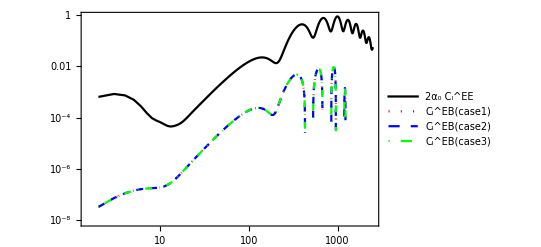

```mathematica
l2ClEB[table_]:= Transpose[{ Transpose[table][[1]],Transpose[table][[4]]}];
l2ClEE2alpha0[table_]  := Transpose[{ Transpose[table][[1]],2alpha0A*Transpose[table][[2]]}];

ListLogLogPlot[
{
l2ClEE2alpha0[Drop[case1,1]],
l2ClEB[Drop[case1,1]],
l2ClEB[Drop[case2,1]],
l2ClEB[Drop[case3,1]]
}
,Joined->True,PlotStyle->{Black, {Red,Dotted},{Blue,Dashed},{Green,DotDashed}},
PlotLegends-> {"2α_0 C_l^EE ", "C_l^EB(case1)", "C_l^EB(case2)", "C_l^EB(case3)"},PlotRange->All,Frame->True
]
```

```mathematica
(*compare 3 cases*)
```

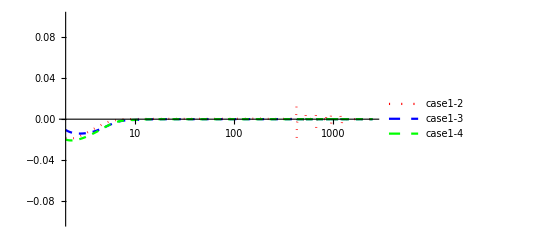

```mathematica
ClEBcase1  = Interpolation[Transpose[{ Transpose[Drop[case1,1]][[1]],Transpose[Drop[case1,1]][[4]]}]];
ClEBcase2 = Interpolation[Transpose[{ Transpose[Drop[case2,1]][[1]],Transpose[Drop[case2,1]][[4]]}]];
ClEBcase3 = Interpolation[Transpose[{ Transpose[Drop[case3,1]][[1]],Transpose[Drop[case3,1]][[4]]}]];
ClEBcase4 = Interpolation[Transpose[{ Transpose[Drop[case4,1]][[1]],Transpose[Drop[case4,1]][[4]]}]];

LogLinearPlot[
{
(ClEBcase2[l]-ClEBcase1[l])/ClEBcase1[l], (ClEBcase3[l]-ClEBcase1[l])/ClEBcase1[l], (ClEBcase4[l]-ClEBcase1[l])/ClEBcase1[l]
}
,{l,2,2500},PlotStyle->{{Red,Dotted},{Blue,Dashed},{Green,Dashed}},
PlotLegends-> {"case1-2", "case1-3","case1-4"},PlotRange->{All,{-0.1,0.1}}
]
```

### m = 10^-27.0

```mathematica
massA = 10^-27.0(*eV*) ;
alpha0A = 0.01;
```

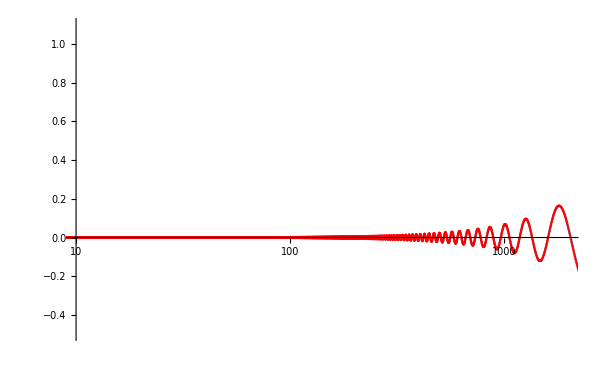

{{l,EE,BB,EB,TB},{2,0.0321975,8.61028×10^-16,-3.47313×10^-9,-7.59247×10^-7},2497,{2500,2.80606,1.95392×10^-6,-0.00172609,0.00204877}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321975,9.51745×10^-16,-3.88532×10^-9,-7.90924×10^-7},2497,{2500,2.80606,1.95695×10^-6,-0.0017273,0.00205078}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321987,9.13091×10^-16,-3.70289×10^-9,-7.79147×10^-7},2497,{2500,2.80606,1.95393×10^-6,-0.00172609,0.00204878}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},2498,{2500,2.80606,1.95393×10^-6,-0.00172609,0.00204878}}
 |  |  |  |

```mathematica
case1 = birefCLASS[massA,2*10^4,alpha0A] 
case2 = birefCLASS[massA,2*10^5,alpha0A] 
case3 = birefCLASSpreciseA[massA,2*10^4,alpha0A] 
case4 = birefCLASSpreciseB[massA,2*10^4,alpha0A]
```

```mathematica
(*show 3 cases*)
```

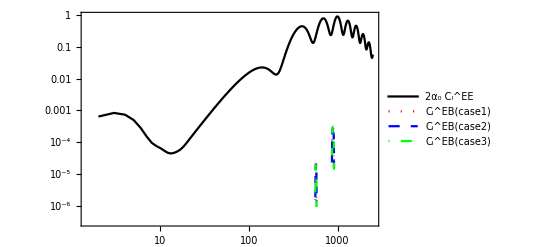

```mathematica
l2ClEB[table_]:= Transpose[{ Transpose[table][[1]],Transpose[table][[4]]}];
l2ClEE2alpha0[table_]  := Transpose[{ Transpose[table][[1]],2alpha0A*Transpose[table][[2]]}];

ListLogLogPlot[
{
l2ClEE2alpha0[Drop[case1,1]],
l2ClEB[Drop[case1,1]],
l2ClEB[Drop[case2,1]],
l2ClEB[Drop[case3,1]]
}
,Joined->True,PlotStyle->{Black, {Red,Dotted},{Blue,Dashed},{Green,DotDashed}},
PlotLegends-> {"2α_0 C_l^EE ", "C_l^EB(case1)", "C_l^EB(case2)", "C_l^EB(case3)"},PlotRange->All,Frame->True
]
```

```mathematica
(*compare 3 cases*)
```

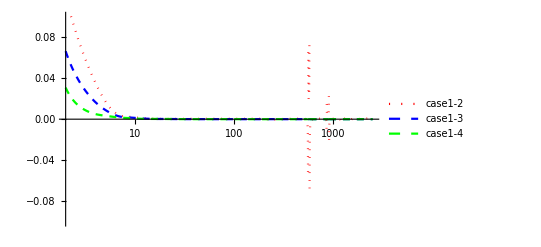

```mathematica
ClEBcase1  = Interpolation[Transpose[{ Transpose[Drop[case1,1]][[1]],Transpose[Drop[case1,1]][[4]]}]];
ClEBcase2 = Interpolation[Transpose[{ Transpose[Drop[case2,1]][[1]],Transpose[Drop[case2,1]][[4]]}]];
ClEBcase3 = Interpolation[Transpose[{ Transpose[Drop[case3,1]][[1]],Transpose[Drop[case3,1]][[4]]}]];
ClEBcase4 = Interpolation[Transpose[{ Transpose[Drop[case4,1]][[1]],Transpose[Drop[case4,1]][[4]]}]];

LogLinearPlot[
{
(ClEBcase2[l]-ClEBcase1[l])/ClEBcase1[l], (ClEBcase3[l]-ClEBcase1[l])/ClEBcase1[l], (ClEBcase4[l]-ClEBcase1[l])/ClEBcase1[l]
}
,{l,2,2500},PlotStyle->{{Red,Dotted},{Blue,Dashed},{Green,Dashed}},
PlotLegends-> {"case1-2", "case1-3","case1-4"},PlotRange->{All,{-0.1,0.1}}
]
```

### m = 10^-27.3

```mathematica
massA = 10^-27.3(*eV*) ;
alpha0A = 0.01;
```

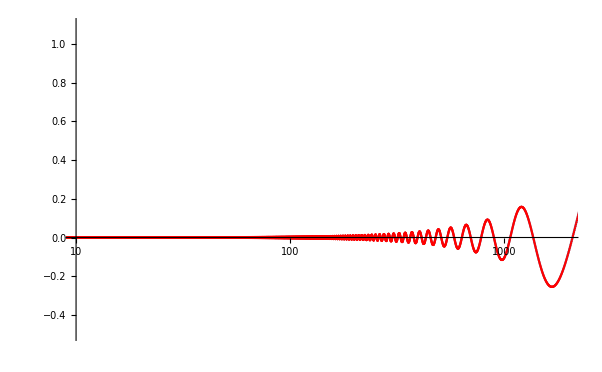

{{l,EE,BB,EB,TB},{2,0.0321975,4.71352×10^-14,-2.87108×10^-8,-5.49958×10^-6},2497,{2500,2.80606,4.71854×10^-6,0.00186224,-0.00976359}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321975,4.61795×10^-14,-2.81442×10^-8,-5.45588×10^-6},2497,{2500,2.80606,4.72018×10^-6,0.0018624,-0.00976549}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321987,4.76305×10^-14,-2.90091×10^-8,-5.52074×10^-6},2497,{2500,2.80606,4.71855×10^-6,0.00186224,-0.00976358}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321992,4.71884×10^-14,-2.87508×10^-8,-5.50181×10^-6},2497,{2500,2.80606,4.71854×10^-6,0.00186224,-0.00976358}}
 |  |  |  |

```mathematica
case1 = birefCLASS[massA,2*10^4,alpha0A] 
case2 = birefCLASS[massA,2*10^5,alpha0A] 
case3 = birefCLASSpreciseA[massA,2*10^4,alpha0A] 
case4 = birefCLASSpreciseB[massA,2*10^4,alpha0A]
```

```mathematica
(*show 3 cases*)
```

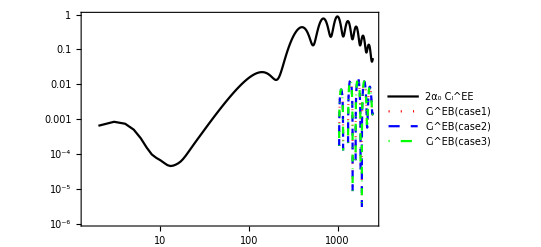

```mathematica
l2ClEB[table_]:= Transpose[{ Transpose[table][[1]],Transpose[table][[4]]}];
l2ClEE2alpha0[table_]  := Transpose[{ Transpose[table][[1]],2alpha0A*Transpose[table][[2]]}];

ListLogLogPlot[
{
l2ClEE2alpha0[Drop[case1,1]],
l2ClEB[Drop[case1,1]],
l2ClEB[Drop[case2,1]],
l2ClEB[Drop[case3,1]]
}
,Joined->True,PlotStyle->{Black, {Red,Dotted},{Blue,Dashed},{Green,DotDashed}},
PlotLegends-> {"2α_0 C_l^EE ", "C_l^EB(case1)", "C_l^EB(case2)", "C_l^EB(case3)"},PlotRange->All,Frame->True
]
```

```mathematica
(*compare 3 cases*)
```

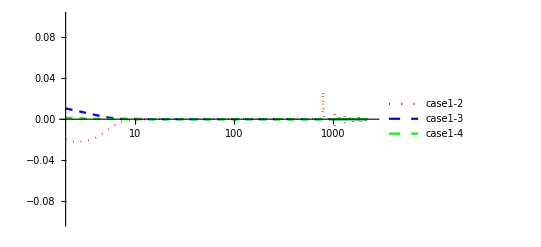

```mathematica
ClEBcase1  = Interpolation[Transpose[{ Transpose[Drop[case1,1]][[1]],Transpose[Drop[case1,1]][[4]]}]];
ClEBcase2 = Interpolation[Transpose[{ Transpose[Drop[case2,1]][[1]],Transpose[Drop[case2,1]][[4]]}]];
ClEBcase3 = Interpolation[Transpose[{ Transpose[Drop[case3,1]][[1]],Transpose[Drop[case3,1]][[4]]}]];
ClEBcase4 = Interpolation[Transpose[{ Transpose[Drop[case4,1]][[1]],Transpose[Drop[case4,1]][[4]]}]];

LogLinearPlot[
{
(ClEBcase2[l]-ClEBcase1[l])/ClEBcase1[l], (ClEBcase3[l]-ClEBcase1[l])/ClEBcase1[l], (ClEBcase4[l]-ClEBcase1[l])/ClEBcase1[l]
}
,{l,2,2500},PlotStyle->{{Red,Dotted},{Blue,Dashed},{Green,Dashed}},
PlotLegends-> {"case1-2", "case1-3","case1-4"},PlotRange->{All,{-0.1,0.1}}
]
```

## Figures

```mathematica
(*We use the following package to produce beautiful figures.
If you do not use MaTeX, eliminate the MaTeX functions in Plot functions.
*)
<<MaTeX`
```

```mathematica
(*1degree= *)
deg1 = Pi/180//N
```

0.0174533

### Useful formulas for plot

```mathematica
(*In the following, `table` refers to the output of the `birefCLASS[]`.*)
```

```mathematica
l2ClEB[table_]:= Drop[Transpose[{ Transpose[table][[1]],Transpose[table][[4]]}],1];
l2ClEE[table_]:= Drop[Transpose[{ Transpose[table][[1]],Transpose[table][[2]]}],1];
```

```mathematica
(* relative angle , evaluated by degree!!!*)
anglefunction[x_] = 1/4 ArcSin[2 x/(1+x^2)];
l2betaeffDeg[table_]:=Drop[ Transpose[{
Transpose[table][[1]],
180/Pi anglefunction@(Transpose[table][[4]]/Transpose[table][[2]])
}],1];
```

### Fig.2: Axion Dynamics

The axion dynamics is shown.

```mathematica
(*masses={10^-30.3,10^-28,10^-31.2,10^-32.3};*)
```

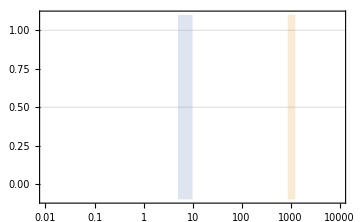

```mathematica
figphiFrame= ListLogLinearPlot[
{    
(*{{5,10^4},{7.82,10^4}},
{{900,10^4},{1200,10^4}}sss*)
{{5,10^4},{10,10^4}},
{{868.0603275188389,10^4},{1244.7711549320286,10^4}}
},
PlotRange->{{10^-2,10^4},{-0.1,1.1}},GridLines->{{}, {0.5,1}},
Joined->True,Filling-> {1-> Bottom,2->Bottom },
FillingStyle->{{Orange},{Cyan}},
Frame->True,ImageSize->Medium,
FrameStyle->Directive[FontSize->13],
FrameLabel->{MaTeX["\\mathrm{redshift}~z",FontSize->15]
,MaTeX["\\phi/\\phi_\\mathrm{in}",FontSize->15]}
]
```

```mathematica
phim280  =solutionPhi[10^-28.0(*eV*)];
phim303  =  solutionPhi[10^-30.3(*eV*)];
phim312  =  solutionPhi[10^-31.2(*eV*)];
phim323  =  solutionPhi[10^-32.3(*eV*)];
```

```mathematica
{phim280[z2time[z]],phim303[z2time[z]],phim312[z2time[z]],phim323[z2time[z]] }/.{z-> 10^-10}
```

{0.000013888,-0.00243583,-0.014773,0.0118622}

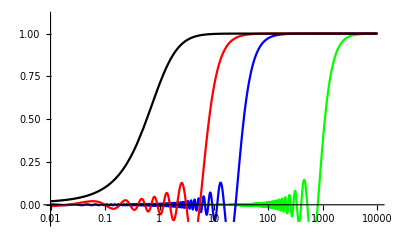

```mathematica
figPhis= LogLinearPlot[
{phim280[z2time[z]],phim303[z2time[z]],phim312[z2time[z]],phim323[z2time[z]] }
, {z,10^-2,10^4},PlotRange->{All,{-0.1,1.1}},
PlotStyle->{Green, Blue, Red,Black},
PlotLegends->LineLegend[
MaTeX[{
"10^{-28.0}~\\mathrm{eV}",
"10^{-30.3}~\\mathrm{eV}",
"10^{-31.2}~\\mathrm{eV}",
"10^{-32.3}~\\mathrm{eV}"
},FontSize->15],LegendLabel->MaTeX["m_\\phi",FontSize->15]]

]
```

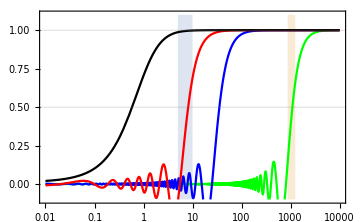

```mathematica
figfielddynamicslist = Show[{figphiFrame,figPhis}]
```

```mathematica
Export["fig_field_dynamics.pdf",figfielddynamicslist]
```

fig_field_dynamics.pdf

### Fig.3: Step function type

```mathematica
(*data*)
rei01rec01 = birefCLASSstep[ 1 deg1,1 deg1,2*10^4]
rei005rec01 = birefCLASSstep[ 0.5 deg1,1 deg1,2*10^4]
rei0rec01= birefCLASSstep[ 0.0,1 deg1,2*10^4]
```

```mathematica
(*Plot ClEB*)
figEBstepalpha=ListLogLogPlot[ 
{l2ClEB[rei01rec01],l2ClEB[rei005rec01],l2ClEB[rei0rec01] },
(*PlotLegends->MaTeX[{
"\\beta_\\mathrm{rei}=0.1,~~~\\beta_\\mathrm{rec}=0.1",
"\\beta_\\mathrm{rei}=0.05,~\\beta_\\mathrm{rec}=0.1",
"\\beta_\\mathrm{rei}=0,~~~~\\beta_\\mathrm{rec}=0.1"
},FontSize->15]
,*)
PlotStyle->{Red,Green,Blue},
PlotRange-> {{2,2500},{10^-6,3}},Joined->True,Frame->True,ImageSize->Medium,
FrameStyle->Directive[FontSize->13],
FrameLabel->{MaTeX["l",FontSize->15]
,MaTeX["l(l+1)C_l^{EB}/(2\\pi)~[\\mu \\mathrm{K}^2]",FontSize->15]}
]
```

```mathematica
Export["fig_EB_for_stepalpha.pdf",figEBstepalpha]
```

```mathematica
(*Plot beta_eff,*)
```

```mathematica
figbetalstepalpha=ListLogLinearPlot[ 
{l2betaeffDeg[rei01rec01] ,l2betaeffDeg[rei005rec01] ,l2betaeffDeg[rei0rec01] },
PlotLegends->Placed[LineLegend[
MaTeX[{
"\\{1~~,1 \\}",
"\\{0.5,1 \\}",
"\\{0~~,1 \\}"
},FontSize->15],LegendLabel->MaTeX["\\{\\beta_\\mathrm{rei}[\\mathrm{deg}],\\beta_\\mathrm{rec}[\\mathrm{deg}]\\}",FontSize->15]],Scaled[{0.7,0.5}]],
PlotStyle->{Red,Green,Blue},
FrameStyle->Directive[FontSize->13],
PlotRange->{{2,2500},{0,1.1}},Joined->True,ImageSize->Medium,Frame->True,
FrameLabel->{MaTeX["l",FontSize->15]
,MaTeX["\\beta_l^\\mathrm{(eff)}~[\\mathrm{deg}]",FontSize->15]}]
```

```mathematica
Export["fig_betal_stepalpha.pdf",figbetalstepalpha]
```

### Fig.4: C_lEB and beta_eff for Axion Dynamics

```mathematica
vNtau = 2*10^4;
valpha0 = 1*deg1;
```

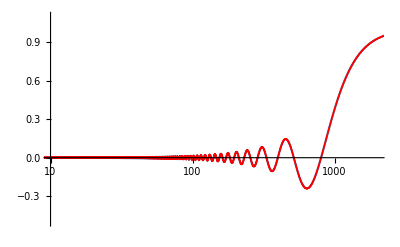

{{l,EE,BB,EB,TB},{2,0.0321975,6.53949×10^-11,1.09145×10^-6,0.000203997},2496,{2499,2.79263,0.00089419,0.0497651,-0.0424015},{2500,2.80516,0.00089901,0.0500157,-0.0424921}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321973,1.6538×10^-9,6.18151×10^-6,0.0009711},2496,{2499,2.7901,0.00342059,0.0976686,-0.0550505},{2500,2.80263,0.00343594,0.0981071,-0.0555111}}
 |  |  |  |

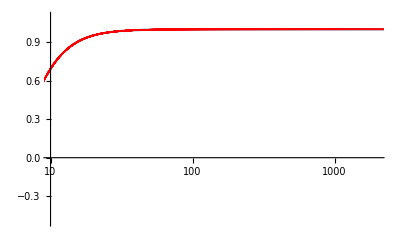

{{l,EE,BB,EB,TB},{2,0.0321962,6.63899×10^-8,0.0000458413,0.00456283},2496,{2499,2.79002,0.00350537,0.09887,-0.0557281},{2500,2.80254,0.00352109,0.0993139,-0.0561943}}
 |  |  |  |

-Graphics-

{{l,EE,BB,EB,TB},{2,0.0321656,0.0000308747,0.000995489,0.0756239},2496,{2499,2.7902,0.00332384,0.0962791,-0.0542659},{2500,2.80272,0.00333875,0.0967114,-0.05472}}
 |  |  |  |

```mathematica
(*data*)
casem280 = birefCLASS[10^-28.0(*eV*),vNtau,valpha0] 
casem303 = birefCLASS[10^-30.3(*eV*),vNtau,valpha0] 
casem312 = birefCLASS[10^-31.2(*eV*),vNtau,valpha0] 
casem323 = birefCLASS[10^-32.3(*eV*),vNtau,valpha0]
```

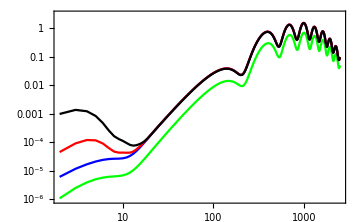

```mathematica
(*Plot ClEB*)
figEBaxionMasses=ListLogLogPlot[ 
{l2ClEB[casem280],l2ClEB[casem303],l2ClEB[casem312] ,l2ClEB[casem323] },
PlotStyle->{Green, Blue, Red,Black},
(*PlotLegends->MaTeX[{
"m_\\phi=10^{-28.0}~\\mathrm{eV}",
"m_\\phi=10^{-30.3}~\\mathrm{eV}",
"m_\\phi=10^{-31.2}~\\mathrm{eV}",
"m_\\phi=10^{-32.3}~\\mathrm{eV}"
},FontSize->15],*)
PlotRange-> {{2,2500},{10^-6,3}},Joined->True,Frame->True,ImageSize->Medium,
FrameStyle->Directive[FontSize->13],
FrameLabel->{MaTeX["l",FontSize->15]
,MaTeX["l(l+1)C_l^{EB}/(2\\pi)~[\\mu \\mathrm{K}^2]",FontSize->15]}
]
```

```mathematica
Export["fig_EB_axion_Masses.pdf",figEBaxionMasses]
```

fig_EB_axion_Masses.pdf

```mathematica
(*Plot beta_eff,*)
```

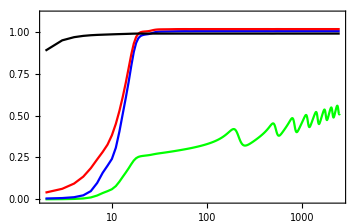

```mathematica
figbetalformass=ListLogLinearPlot[ 
{l2betaeffDeg[casem280],l2betaeffDeg[casem303],l2betaeffDeg[casem312] ,l2betaeffDeg[casem323] },
PlotStyle->{Green, Blue, Red,Black},
PlotLegends->LineLegend[
MaTeX[{
"10^{-28.0}~\\mathrm{eV}",
"10^{-30.3}~\\mathrm{eV}",
"10^{-31.2}~\\mathrm{eV}",
"10^{-32.3}~\\mathrm{eV}"
},FontSize->15],LegendLabel->MaTeX["m_\\phi",FontSize->15]]
,
FrameStyle->Directive[FontSize->13],
PlotRange->{{2,2500},{0,1.1}},Joined->True,ImageSize->Medium,Frame->True,
FrameLabel->{MaTeX["l",FontSize->15]
,MaTeX["\\beta_l^\\mathrm{(eff)}~[\\mathrm{deg}]",FontSize->15]}
]
```

```mathematica
Export["fig_betal_for_mass.pdf",figbetalformass]
```

fig_betal_for_mass.pdf

### Fig.5: ratio of rotation angles

We calculate the effective rotation angle for various axion masses,

```mathematica
vNtau = 2*10^4;
valpha0 =0.0174533 (*=1deg*);
```

```mathematica
masslist=Table[10^i(*eV*),{i,-34,-28,0.2}]
Length[masslist]
```

{1.×10^-34,1.58489×10^-34,2.51189×10^-34,3.98107×10^-34,6.30957×10^-34,1.×10^-33,1.58489×10^-33,2.51189×10^-33,3.98107×10^-33,6.30957×10^-33,1.×10^-32,1.58489×10^-32,2.51189×10^-32,3.98107×10^-32,6.30957×10^-32,1.×10^-31,1.58489×10^-31,2.51189×10^-31,3.98107×10^-31,6.30957×10^-31,1.×10^-30,1.58489×10^-30,2.51189×10^-30,3.98107×10^-30,6.30957×10^-30,1.×10^-29,1.58489×10^-29,2.51189×10^-29,3.98107×10^-29,6.30957×10^-29,1.×10^-28}

31

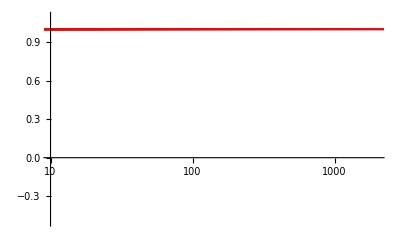

-Graphics-

-Graphics-

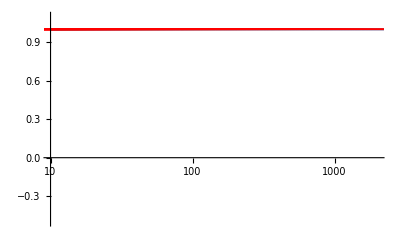

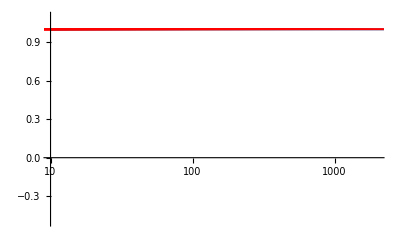

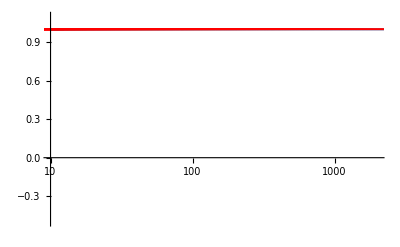

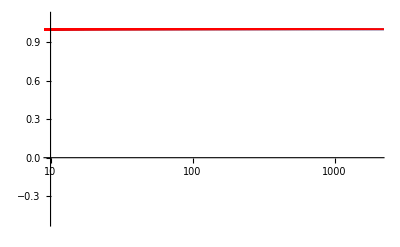

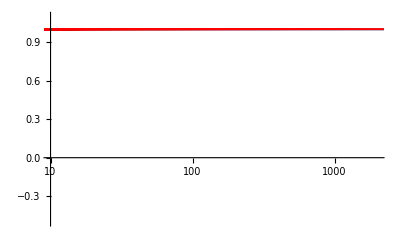

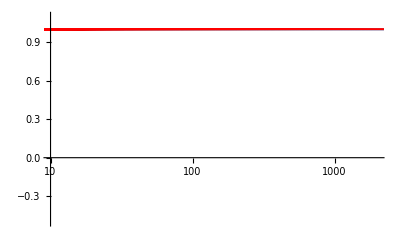

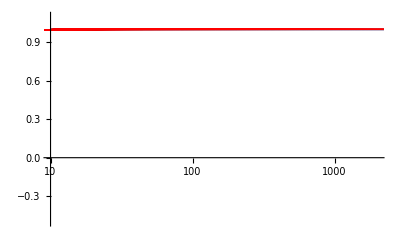

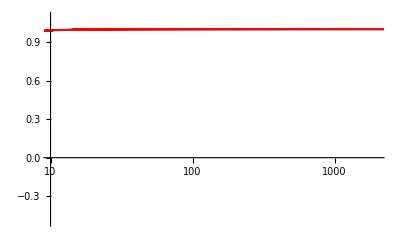

-Graphics-

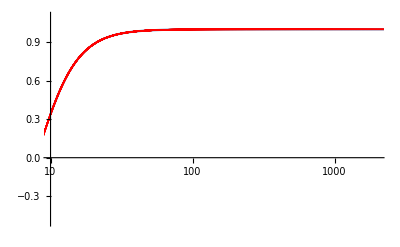

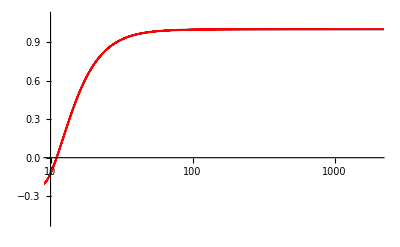

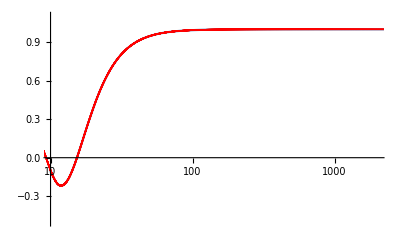

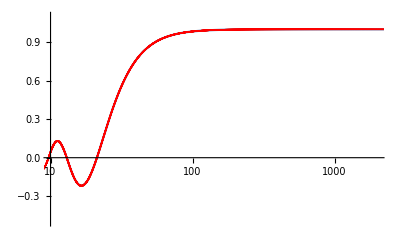

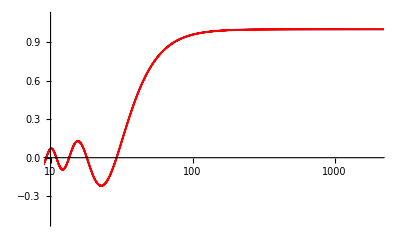

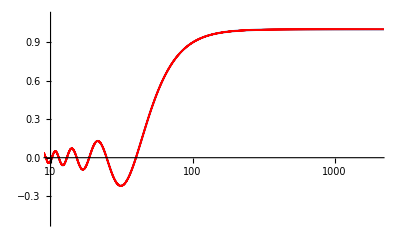

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
cases = Table[birefCLASS[masslist[[i]],vNtau,valpha0] ,{i,1,Length[masslist]} ];
```

```mathematica
betaratioEdge[table_]:=
Module[{betalTable},
betalTable= l2betaeffDeg[table];
(*Print[{betalTable[[2-1]],betalTable[[500-1]]}];*)
betalTable[[2-1,2]]/betalTable[[500-1,2]]
]
```

```mathematica
betaratioMean[table_]:=
Module[{betalTable},
betalTable= l2betaeffDeg[table];
Mean[betalTable[[1;;9,2]]]/Mean[betalTable[[10;;499,2]]]
]
```

```mathematica
Table[betaratioEdge[cases[[i]]],{i,1,Length[masslist]} ]
```

{0.929205,0.929188,0.929147,0.929054,0.928801,0.928176,0.926579,0.922381,0.910546,0.871223,0.712397,0.578071,0.381018,0.146873,0.0402001,-0.0302163,0.00952674,0.00409531,0.0079494,0.00357516,0.00289438,0.00464298,0.00361161,0.00364685,0.00346909,0.00360763,0.00329382,0.0031654,0.00298224,0.00269043,0.00214494}

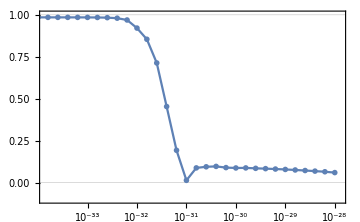

```mathematica
figbetaratio=ListLogLinearPlot[
{
(*Table[{masslist[[i]],betaratioEdge[cases[[i]]]},{i,1,Length[masslist]} ],*)
Table[{masslist[[i]],betaratioMean[cases[[i]]]},{i,1,Length[masslist]} ]
},
PlotRange->{{10^-33.85,10^-27.9},{-0.1,1}},
Joined->True,PlotMarkers->"OpenMarkers",
Frame->True,ImageSize->Medium,
FrameStyle->Directive[FontSize->13],
GridLines->{{},{0,1}},
(*PlotLegends->MaTeX[{"\\mathrm{edge}","\\mathrm{mean}"},FontSize->15],*)
FrameLabel->{MaTeX["\\mathrm{mass}~[\\mathrm{eV}]",FontSize->15],
(*MaTeX["\\big[\\beta_\\mathrm{rei}/\\beta_\\mathrm{rec}\\big]",FontSize->15]*)
MaTeX["\\mathrm{Ratio~of~rotation~angles}",FontSize->15]
}
]
```

```mathematica
Export["fig_betaratio.pdf",figbetaratio]
```

fig_betaratio.pdf

### Fig.6: C_lEB for m < 10^-28 eV

```mathematica
vNtau = 2*10^4;
valpha0 = deg1;
```

```mathematica
(*ClEBm288, ClEBm284, ClEBm280, ClEBm279*)
```

```mathematica
(*data*)
casem288 = birefCLASS[10^-28.8(*eV*),vNtau,valpha0] 
Export["casem288.csv",casem288]
(*casem288=Import["casem288.csv","CSV"]*)
```

```mathematica
casem279 = birefCLASS[10^-27.9(*eV*),vNtau,valpha0] 
Export["casem279.csv",casem279]
(*casem279=Import["casem279.csv","CSV"]*)
```

```mathematica
casem278 = birefCLASS[10^-27.8(*eV*),vNtau,valpha0] 
Export["casem278.csv",casem278]
(*casem278=Import["casem278.csv","CSV"]*)
```

```mathematica
casem277 = birefCLASS[10^-27.7(*eV*),vNtau,valpha0] 
Export["casem277.csv",casem277]
(*casem277=Import["casem277.csv","CSV"]*)
```

```mathematica
(*find 3nd peaks *)
ThirdPeak[table_] := Module[{functionl2ClEB,lpeak},
functionl2ClEB = Interpolation[l2ClEB[table]];
lpeak=l/.FindMaximum[functionl2ClEB[l],{l,980}][[2]];
{lpeak,functionl2ClEB[lpeak] }
]
```

```mathematica
figverticals=ListPlot[
{
{{ ThirdPeak[casem288] [[1]],0.}, ThirdPeak[casem288] },
{{ ThirdPeak[casem279] [[1]],0.}, ThirdPeak[casem279] }(*,
{{ ThirdPeak[casem278] [[1]],0.}, ThirdPeak[casem278] },
{{ ThirdPeak[casem277] [[1]],0.}, ThirdPeak[casem277] }*)
},
PlotRange->{{100,1500},{-0.4,1.6}},
Frame->True,ImageSize->Medium,Joined->True,
PlotStyle->{{Black,Dotted}, {Red,Dotted},{Blue,Dotted},{Green,Dotted}}
]
```

```mathematica
(*Fig.7 main*)
figClEBHeavy=Show[
 ListPlot[
{l2ClEB[casem288],l2ClEB[casem279],l2ClEB[casem278] ,l2ClEB[casem277] },
PlotRange->{{2,2500},{-0.4,1.6}},
Frame->True,ImageSize->Medium,Joined->True,
PlotStyle->{Black, Red,Blue,Green,Orange},
FrameStyle->Directive[FontSize->13],
FrameLabel->{MaTeX["l",FontSize->15]
,MaTeX["l(l+1)C_l^{EB}/(2\\pi)~[\\mu \\mathrm{K}^2]",FontSize->15]}(*,
PlotLegends->
MaTeX[{
"m_\\phi=10^{-28.8}~\\mathrm{eV}",
"m_\\phi=10^{-27.9}~\\mathrm{eV}",
"m_\\phi=10^{-27.8}~\\mathrm{eV}",
"m_\\phi=10^{-27.7}~\\mathrm{eV}"
},FontSize->15]*)
]
,
figverticals
]
```

```mathematica
phim288  =solutionPhi[10^-28.8(*eV*)];
phim279  =  solutionPhi[10^-27.9(*eV*)];
```

```mathematica
phim278  =  solutionPhi[10^-27.8(*eV*)];
phim277 =  solutionPhi[10^-27.7(*eV*)];
```

```mathematica
figPhis= LogLinearPlot[
{phim288[z2time[z]],phim279[z2time[z]],phim278[z2time[z]],phim277[z2time[z]] }
, {z,10^-2,10^4},PlotRange->{{3*10^2,10^3.5},{-0.3,1.1}},
PlotStyle->{Black, Red,Blue,Green,Orange},
FrameStyle->Directive[FontSize->13],

PlotLegends->LineLegend[
MaTeX[{
"10^{-28.8}~\\mathrm{eV}",
"10^{-27.9}~\\mathrm{eV}",
"10^{-27.8}~\\mathrm{eV}",
"10^{-27.7}~\\mathrm{eV}"
},FontSize->15],LegendLabel->MaTeX["m_\\phi",FontSize->15]]
]
```

```mathematica
figphiFrame= ListLogLinearPlot[
{    
{{5,10^4},{10,10^4}},
{{868.0603275188389,10^4},{1244.7711549320286,10^4}}
},
PlotRange->{{600,1900},{-0.3,1.1}},GridLines->{{}, {0.5,1}},
Joined->True,Filling-> {1-> Bottom,2->Bottom },
FillingStyle->{{Orange},{Cyan}},
Frame->True,ImageSize->Medium,
FrameStyle->Directive[FontSize->13],
FrameLabel->{MaTeX["\\mathrm{redshift}~z",FontSize->15]
,MaTeX["\\phi/\\phi_\\mathrm{in}",FontSize->15]}
];
figfielddynamicslist = Show[{figphiFrame,figPhis}]
```

```mathematica
Export["fig_compare_Clforms.pdf",figClEBHeavy]
```

```mathematica
Export["fig_compare_Clforms_axionDynamics.pdf",figfielddynamicslist]
```

### Fig.7: beta_eff for m = 10^(-27.9,27.8)eV

```mathematica
vNtau = 2*10^4;
valpha0 = deg1;
```

```mathematica
(*evaluate*)
(*casem278 = birefCLASS[10^-27.8(*eV*),vNtau,valpha0] 
casem279 = birefCLASS[10^-27.9(*eV*),vNtau,valpha0] *)

casem278=Import["casem278.csv","CSV"]
casem279=Import["casem279.csv","CSV"]
```

{{l,EE,BB,EB,TB},{2,0.0321975,2.61829×10^-12,-2.17352×10^-7,-0.0000408027},2496,{2499,2.7935,0.0000229024,0.00502866,-0.0219452},{2500,2.80604,0.0000228046,0.00508446,-0.021766}}
 |  |  |  |

{{l,EE,BB,EB,TB},{2,0.0321975,9.27721×10^-12,4.17159×10^-7,0.0000765391},2496,{2499,2.79321,0.000314045,0.0290663,-0.0344696},{2500,2.80575,0.000315881,0.0292302,-0.0344216}}
 |  |  |  |

```mathematica
Export["solphi279.m",solutionPhi[10^-27.9]]
```

solphi279.m

```mathematica
phim279=Import["solphi279.m"]
```

-7
InterpolatingFunction[{{2.31325 10  , 4229.47}}, <>]

```mathematica
Export["solphi278.m",solutionPhi[10^-27.8]]
```

solphi278.m

```mathematica
phim278 = Import["solphi278.m"]
```

-7
InterpolatingFunction[{{2.31325 10  , 4229.47}}, <>]

```mathematica
(*visibility function*)
```

```mathematica
(*g_vis: visibility function (numerical)*)
thermal=Import["data_axion/CLASS_data_thermodynamics.dat"];
thermal[[11]]
thermo = Drop[thermal,11];
tableTau2g = Transpose[{
Transpose[thermo][[2]],Transpose[thermo][[6]]
}];
Tau2g = Interpolation[tableTau2g];
```

{#,1:z,2:conf.,time,[Mpc],3:x_e,4:kappa',[Mpc^-1],5:exp(-kappa),6:g,[Mpc^-1],7:Tb,[K],8:w_b,9:c_b^2,10:tau_d}

```mathematica
(*Confirm normalization *)
NIntegrate[Tau2g[tau],{tau,z2tau[10^5],z2tau[0]}]
```

0.999999

```mathematica
(*estimate effective rotation angle *)
```

```mathematica
(*<beta> with g_vis*)
normalizationfactor = NIntegrate[Tau2g[tau],{tau,z2tau[10^5],z2tau[10]}]
braketphiNum =1/normalizationfactor NIntegrate[Tau2g[tau]phim278[tau2time[tau]],{tau,z2tau[10^5],z2tau[10]},WorkingPrecision->3MachinePrecision]
braketBetagvis278 =-deg1(phim278[z2time[0]]-braketphiNum )
```

0.945531

NIntegrate::slwcon: 数値積分の収束が遅すぎます．特異性がある，積分の値がゼロ，被積分関数が激しく振動する，あるいはWorkingPrecisionが小さすぎるのいずれかが原因である可能性があります．

NIntegrate::ncvb: NIntegrateが{tau} = {340.8504721182822639846308902606364894902766545801843059556785006336896418542337858827850400772982}の近傍のtauで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として-0.002161186523838331948644528283264763509980323238159569001494000749515777483096778801011074516844719と3.871162677533743985111915425568358975821768089139758932858687641767257922995407748235361151631331×10^-11を得ました．

-0.00228568

-0.0000397615

```mathematica
braketphiNum =1/normalizationfactor NIntegrate[Tau2g[tau]phim279[tau2time[tau]],{tau,z2tau[10^5],z2tau[10]},WorkingPrecision->3MachinePrecision]
braketBetagvis279 =-deg1(phim279[z2time[0]]-braketphiNum )
```

NIntegrate::ncvb: NIntegrateが{tau} = {287.7297845573798261452644088760228095656117903832393339712905328981740147788478673806744897289529}の近傍のtauで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として0.2057378898943757287950601579254308905774262940228733129476579490176839987681939422547149352066124と3.769601654455058880561488256159300880235950775422375833139734267212649761467368973950831689588896×10^-11を得ました．

0.21759

0.00379785

```mathematica
(*Fig*)
```

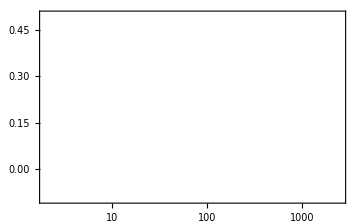

```mathematica
figFlames=ListLogLinearPlot[ 
{{0,-1000},{1,-1001}},
PlotRange->{{2,2500},{-0.1,0.5}},
Frame->True,ImageSize->Medium,
FrameStyle->Directive[FontSize->13],
FrameLabel->{MaTeX["l",FontSize->15]
,MaTeX["\\beta_l^\\mathrm{(eff)}~[\\mathrm{deg}]",FontSize->15]},
Axes-> False
]
```

```mathematica
figbetalm279Compare =Show[{figFlames,
ListLogLinearPlot[ 
{
l2betaeffDeg[casem279],
{{2,180/Pi braketBetagvis279},{2500,180/Pi braketBetagvis279}}
},
PlotRange->All,Joined->True,
PlotStyle->{Red,(*{Black,Dotted},*)Black}(*,
PlotLegends->
Placed[{
MaTeX["\\beta_l^\\mathrm{(eff)}",FontSize->15],
(*MaTeX["\\left<\\beta \\right> \\mathrm{~with~}\\mathcal{V}(T)",FontSize->15],*)
MaTeX["\\left<\\beta \\right>",FontSize->15]
},Scaled[{0.5,0.8}]]*)

]
},PlotLabel-> MaTeX["m_\\phi=10^{-27.9}~\\mathrm{eV}",FontSize->15]]
```

-Graphics-

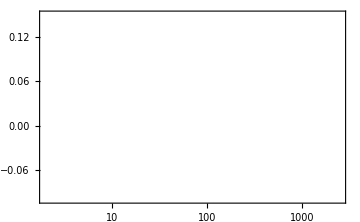

```mathematica
figFlames=ListLogLinearPlot[ 
{{0,-1000},{1,-1001}},
PlotRange->{{2,2500},{-0.1,0.15}},
Frame->True,ImageSize->Medium,
FrameStyle->Directive[FontSize->13],
FrameLabel->{MaTeX["l",FontSize->15]
,MaTeX["\\beta_l^\\mathrm{(eff)}~[\\mathrm{deg}]",FontSize->15]},
Axes-> False
]
```

```mathematica
figbetalm278Compare =Show[{figFlames,
ListLogLinearPlot[ 
{
l2betaeffDeg[casem278],
{{2,180/Pi braketBetagvis278},{2500,180/Pi braketBetagvis278}}
},
PlotRange->All,Joined->True,
PlotStyle->{Blue,Black}(*,
PlotLegends->
Placed[{
None,
MaTeX["\\left<\\beta \\right> \\mathrm{~with~}\\mathcal{V}(T)",FontSize->15],
MaTeX["\\left<\\beta \\right> \\mathrm{~with~}g_\\mathrm{vis}(\\eta)",FontSize->15]
},Scaled[{0.5,0.8}]]*)

]
},PlotLabel-> MaTeX["m_\\phi=10^{-27.8}~\\mathrm{eV}",FontSize->15]]
```

-Graphics-

```mathematica
Export["fig_betal_m278_compare.pdf",figbetalm278Compare]
Export["fig_betal_m279_compare.pdf",figbetalm279Compare]
```

fig_betal_m278_compare.pdf

fig_betal_m279_compare.pdf

### FORECAST data: Cl

```mathematica
vNtau = 2*10^4;
valpha0 =0.0174533 (*=1deg*);
```

```mathematica
ExportCltable[mass_(*eV*)]:=Module[{case},
case= birefCLASS[mass(*eV*),vNtau,valpha0] ;
Export["data_axion/data_Cl/v9_m"<>ToString[Round[-100*Log[10,mass]]]<>".dat",case]
]
```

```mathematica
(*masslist=Table[10^i(*eV*),{i,-33,-27.3,0.05}]*)

masslist=Table[10^i(*eV*),{i,-27.75,-27.3,0.1}]
Length[masslist]
```

```mathematica
masslist[[1]]
```

```mathematica
For[i=1,i<Length[masslist]+1,i++,
Print[i];
ExportCltable[masslist[[i]](*eV*)];
]
```

### FORECAST data: <beta_rec>

```mathematica
valpha0 =0.0174533 (*=1deg*);
```

```mathematica
thermal=Import["data_axion/CLASS_data_thermodynamics.dat"];
thermal[[11]]
thermo = Drop[thermal,11];
tableTau2g = Transpose[{
Transpose[thermo][[2]],Transpose[thermo][[6]]
}];
Tau2g = Interpolation[tableTau2g];
normalizationfactor = NIntegrate[Tau2g[tau],{tau,z2tau[10^5],z2tau[10]}]
```

```mathematica
betarecEff[mass_] :=Module[{phi0,braketphiLSS},
(*prepare axion dynamics*)
phi0  =solutionPhi[mass(*eV*)];

(*g_vis: visibility function (numerical)*)
braketphiLSS =1/normalizationfactor NIntegrate[Tau2g[tau]phi0[tau2time[tau]],{tau,z2tau[10^5],z2tau[10]},WorkingPrecision->3MachinePrecision];
-valpha0(phi0[z2time[0]]-braketphiLSS ) 
]
```

```mathematica
(*example*)
betarecEff[10^-28]/valpha0
```

```mathematica
0.04282135114320917/0.1
```

```mathematica
(*make table*)
```

```mathematica
masslist=Table[10^i(*eV*),{i,-33,-27.3,0.05}]
Length[masslist]
```

```mathematica
betarecEffList = Table[
{ToString[Round[-100*Log[10,masslist[[i]]]]],
betarecEff[masslist[[i]]]
},{i,1,Length[masslist] }]
```

```mathematica
Export["list_betarec.dat",betarecEffList]
```